```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{1}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
Table[{ω,tr[ω,0.0001,1,0]},{ω,0,3,0.01}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999999},{0.28,0.999999},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.00001},{0.41,1.00014},{0.42,1.99993},{0.43,1.99999},{0.44,2.},{0.45,2.},{0.46,2.},{0.47,2.},{0.48,2.},{0.49,2.},{0.5,2.},{0.51,2.},{0.52,2.},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.},{0.78,2.},{0.79,2.},{0.8,2.},{0.81,2.},{0.82,2.},{0.83,2.00001},{0.84,2.00004},{0.85,2.9995},{0.86,2.99998},{0.87,2.99999},{0.88,3.},{0.89,3.},{0.9,3.},{0.91,3.},{0.92,3.},{0.93,3.},{0.94,3.},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,3.},{1.61,3.},{1.62,3.},{1.63,3.},{1.64,3.},{1.65,3.},{1.66,3.},{1.67,3.},{1.68,3.},{1.69,3.},{1.7,3.},{1.71,3.},{1.72,3.},{1.73,3.},{1.74,3.},{1.75,2.99999},{1.76,2.99991},{1.77,2.00012},{1.78,2.00001},{1.79,2.},{1.8,2.},{1.81,2.},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,2.},{2.22,2.},{2.23,2.},{2.24,2.},{2.25,2.},{2.26,2.},{2.27,2.},{2.28,2.},{2.29,2.},{2.3,2.},{2.31,2.},{2.32,2.},{2.33,2.},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,2.},{2.39,2.},{2.4,1.99999},{2.41,1.99986},{2.42,1.00007},{2.43,1.00001},{2.44,1.},{2.45,1.},{2.46,1.},{2.47,1.},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,1.},{2.55,1.},{2.56,1.},{2.57,1.},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,1.},{2.64,1.},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
m1[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
m2[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp2,imp,imp,imp,imp,imp,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
Table[{ω,Mean[ParallelTable[Mean[{m1[ω,0.5],m2[ω,0.5]}],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,3.59474×10^-7},{0.01,7.9274×10^-7},{0.02,2.01165×10^-6},{0.03,4.02829×10^-6},{0.04,6.09589×10^-6},{0.05,0.0000103916},{0.06,0.0000163099},{0.07,0.000020001},{0.08,0.0000284491},{0.09,0.0000379956},{0.1,0.000043907},{0.11,0.0000539018},{0.12,0.0000667267},{0.13,0.0000809138},{0.14,0.000103184},{0.15,0.000122881},{0.16,0.000143477},{0.17,0.000176508},{0.18,0.000239032},{0.19,0.000323716},{0.2,0.000445054},{0.21,0.000674297},{0.22,0.00134979},{0.23,0.00410183},{0.24,0.735334},{0.25,0.891053},{0.26,0.933493},{0.27,0.950754},{0.28,0.958647},{0.29,0.964349},{0.3,0.967625},{0.31,0.969256},{0.32,0.971797},{0.33,0.972746},{0.34,0.973931},{0.35,0.974746},{0.36,0.973935},{0.37,0.973369},{0.38,0.970751},{0.39,0.965719},{0.4,0.950991},{0.41,0.868255},{0.42,1.38722},{0.43,1.70841},{0.44,1.80444},{0.45,1.85146},{0.46,1.87578},{0.47,1.89531},{0.48,1.90492},{0.49,1.91363},{0.5,1.91888},{0.51,1.92517},{0.52,1.93047},{0.53,1.93408},{0.54,1.93825},{0.55,1.93961},{0.56,1.94088},{0.57,1.94335},{0.58,1.94556},{0.59,1.94762},{0.6,1.9485},{0.61,1.95041},{0.62,1.95083},{0.63,1.95241},{0.64,1.95306},{0.65,1.95416},{0.66,1.95443},{0.67,1.95499},{0.68,1.95598},{0.69,1.95761},{0.7,1.95737},{0.71,1.9582},{0.72,1.95794},{0.73,1.95919},{0.74,1.95944},{0.75,1.95977},{0.76,1.95942},{0.77,1.95983},{0.78,1.95938},{0.79,1.95903},{0.8,1.95848},{0.81,1.95679},{0.82,1.95169},{0.83,1.94086},{0.84,1.8956},{0.85,1.70325},{0.86,2.48948},{0.87,2.67593},{0.88,2.75701},{0.89,2.79444},{0.9,2.82447},{0.91,2.84404},{0.92,2.85818},{0.93,2.8717},{0.94,2.87978},{0.95,2.8922},{0.96,2.89747},{0.97,2.90613},{0.98,2.91289},{0.99,2.91809},{1.,2.91847},{1.01,2.92154},{1.02,2.91276},{1.03,2.88225},{1.04,2.79481},{1.05,2.54453},{1.06,2.10939},{1.07,2.12016},{1.08,2.38173},{1.09,2.54257},{1.1,2.64138},{1.11,2.6985},{1.12,2.73913},{1.13,2.7611},{1.14,2.77808},{1.15,2.79312},{1.16,2.8053},{1.17,2.81382},{1.18,2.82162},{1.19,2.82591},{1.2,2.82955},{1.21,2.83397},{1.22,2.83652},{1.23,2.83942},{1.24,2.84105},{1.25,2.84414},{1.26,2.84492},{1.27,2.84678},{1.28,2.84739},{1.29,2.84821},{1.3,2.84763},{1.31,2.84811},{1.32,2.84941},{1.33,2.84817},{1.34,2.84764},{1.35,2.84722},{1.36,2.8487},{1.37,2.84709},{1.38,2.84678},{1.39,2.84511},{1.4,2.84432},{1.41,2.8445},{1.42,2.84325},{1.43,2.84109},{1.44,2.84017},{1.45,2.83737},{1.46,2.83608},{1.47,2.83274},{1.48,2.83249},{1.49,2.8293},{1.5,2.8265},{1.51,2.8238},{1.52,2.81988},{1.53,2.81584},{1.54,2.81391},{1.55,2.8071},{1.56,2.80614},{1.57,2.79765},{1.58,2.79282},{1.59,2.78868},{1.6,2.78084},{1.61,2.7724},{1.62,2.76523},{1.63,2.7548},{1.64,2.74416},{1.65,2.73081},{1.66,2.7193},{1.67,2.70113},{1.68,2.68411},{1.69,2.65485},{1.7,2.62952},{1.71,2.58647},{1.72,2.54245},{1.73,2.47216},{1.74,2.36398},{1.75,2.17715},{1.76,1.66417},{1.77,2.45548},{1.78,2.52016},{1.79,1.84757},{1.8,1.75283},{1.81,1.81296},{1.82,1.85351},{1.83,1.87736},{1.84,1.8918},{1.85,1.89929},{1.86,1.90672},{1.87,1.91081},{1.88,1.91291},{1.89,1.91606},{1.9,1.91737},{1.91,1.91942},{1.92,1.91945},{1.93,1.922},{1.94,1.92175},{1.95,1.92121},{1.96,1.92139},{1.97,1.9207},{1.98,1.92092},{1.99,1.92142},{2.,1.92025},{2.01,1.91985},{2.02,1.92047},{2.03,1.91868},{2.04,1.91731},{2.05,1.91706},{2.06,1.91707},{2.07,1.9148},{2.08,1.91542},{2.09,1.91335},{2.1,1.91292},{2.11,1.90976},{2.12,1.9081},{2.13,1.90708},{2.14,1.90583},{2.15,1.90483},{2.16,1.90235},{2.17,1.90108},{2.18,1.89792},{2.19,1.89571},{2.2,1.89073},{2.21,1.88856},{2.22,1.8863},{2.23,1.88129},{2.24,1.87922},{2.25,1.87678},{2.26,1.86816},{2.27,1.86333},{2.28,1.85872},{2.29,1.85205},{2.3,1.84301},{2.31,1.83698},{2.32,1.8202},{2.33,1.81091},{2.34,1.79451},{2.35,1.77415},{2.36,1.74845},{2.37,1.72004},{2.38,1.67191},{2.39,1.60514},{2.4,1.47138},{2.41,1.13873},{2.42,1.72979},{2.43,1.63985},{2.44,0.872307},{2.45,0.888994},{2.46,0.915399},{2.47,0.93143},{2.48,0.939712},{2.49,0.946073},{2.5,0.948409},{2.51,0.950272},{2.52,0.951034},{2.53,0.951652},{2.54,0.952259},{2.55,0.95303},{2.56,0.952541},{2.57,0.950746},{2.58,0.951819},{2.59,0.950824},{2.6,0.949669},{2.61,0.946979},{2.62,0.946685},{2.63,0.945197},{2.64,0.942654},{2.65,0.94185},{2.66,0.939843},{2.67,0.938342},{2.68,0.935554},{2.69,0.929703},{2.7,0.928555},{2.71,0.924832},{2.72,0.921136},{2.73,0.915843},{2.74,0.909079},{2.75,0.900899},{2.76,0.895655},{2.77,0.883865},{2.78,0.873821},{2.79,0.851306},{2.8,0.835376},{2.81,0.804333},{2.82,0.759919},{2.83,0.687331},{2.84,0.542746},{2.85,0.344123},{2.86,0.0110094},{2.87,0.000973799},{2.88,0.0000983599},{2.89,0.0000480418},{2.9,0.000149574},{2.91,0.0000577391},{2.92,0.0000624447},{2.93,0.0000565682},{2.94,0.000042613},{2.95,0.0000264888},{2.96,0.0000117149},{2.97,0.0000244911},{2.98,0.000021575},{2.99,0.0000120213},{3.,0.0000189234}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/1per.dat",%31]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/1per.dat

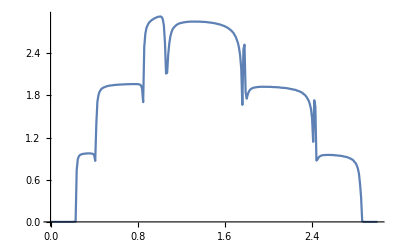

```mathematica
ListPlot[%31,Joined->True]
```

```mathematica
m3[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp2,imp3,imp,imp,imp,imp,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/2per.dat",%34]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/2per.dat

```mathematica
Table[{ω,Mean[ParallelTable[m3[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,1.2216×10^-6},{0.01,1.19192×10^-6},{0.02,2.5963×10^-6},{0.03,5.47093×10^-6},{0.04,7.51782×10^-6},{0.05,0.0000104869},{0.06,0.0000168009},{0.07,0.0000192563},{0.08,0.0000277875},{0.09,0.0000339932},{0.1,0.0000469697},{0.11,0.0000611885},{0.12,0.000065247},{0.13,0.000080929},{0.14,0.000101423},{0.15,0.000105868},{0.16,0.000136724},{0.17,0.000173643},{0.18,0.000233671},{0.19,0.000217841},{0.2,0.00036604},{0.21,0.00050527},{0.22,0.000882828},{0.23,0.00274894},{0.24,0.403743},{0.25,0.727379},{0.26,0.854481},{0.27,0.893294},{0.28,0.917437},{0.29,0.929689},{0.3,0.935733},{0.31,0.939619},{0.32,0.944848},{0.33,0.946877},{0.34,0.94997},{0.35,0.948644},{0.36,0.948823},{0.37,0.948171},{0.38,0.943474},{0.39,0.935104},{0.4,0.911958},{0.41,0.805603},{0.42,0.916057},{0.43,1.38008},{0.44,1.59562},{0.45,1.69347},{0.46,1.75264},{0.47,1.78872},{0.48,1.81299},{0.49,1.83065},{0.5,1.84631},{0.51,1.85574},{0.52,1.86237},{0.53,1.86939},{0.54,1.8764},{0.55,1.88278},{0.56,1.88775},{0.57,1.89125},{0.58,1.89527},{0.59,1.89886},{0.6,1.89824},{0.61,1.90262},{0.62,1.90408},{0.63,1.90456},{0.64,1.90825},{0.65,1.90857},{0.66,1.90991},{0.67,1.91368},{0.68,1.91274},{0.69,1.9174},{0.7,1.91809},{0.71,1.9161},{0.72,1.91821},{0.73,1.91893},{0.74,1.91825},{0.75,1.92074},{0.76,1.92025},{0.77,1.91886},{0.78,1.92087},{0.79,1.92082},{0.8,1.91904},{0.81,1.91425},{0.82,1.90546},{0.83,1.89051},{0.84,1.81717},{0.85,1.20361},{0.86,1.99453},{0.87,2.34201},{0.88,2.50657},{0.89,2.60347},{0.9,2.6571},{0.91,2.69525},{0.92,2.72358},{0.93,2.74647},{0.94,2.76544},{0.95,2.78676},{0.96,2.80541},{0.97,2.81116},{0.98,2.82572},{0.99,2.84272},{1.,2.84629},{1.01,2.84524},{1.02,2.8282},{1.03,2.77268},{1.04,2.61138},{1.05,2.17207},{1.06,1.51196},{1.07,1.52238},{1.08,1.90777},{1.09,2.18526},{1.1,2.342},{1.11,2.43717},{1.12,2.5053},{1.13,2.55217},{1.14,2.58529},{1.15,2.60802},{1.16,2.62842},{1.17,2.64035},{1.18,2.65799},{1.19,2.67045},{1.2,2.67273},{1.21,2.67973},{1.22,2.69211},{1.23,2.69273},{1.24,2.69251},{1.25,2.70119},{1.26,2.70517},{1.27,2.70663},{1.28,2.70971},{1.29,2.70429},{1.3,2.70862},{1.31,2.7133},{1.32,2.70732},{1.33,2.70977},{1.34,2.71276},{1.35,2.71113},{1.36,2.71069},{1.37,2.70744},{1.38,2.70436},{1.39,2.70581},{1.4,2.70268},{1.41,2.70175},{1.42,2.69758},{1.43,2.69675},{1.44,2.69256},{1.45,2.69477},{1.46,2.68481},{1.47,2.68427},{1.48,2.67774},{1.49,2.67745},{1.5,2.67213},{1.51,2.66517},{1.52,2.65707},{1.53,2.65526},{1.54,2.64543},{1.55,2.6369},{1.56,2.63029},{1.57,2.61717},{1.58,2.61443},{1.59,2.59637},{1.6,2.59742},{1.61,2.57945},{1.62,2.56552},{1.63,2.54766},{1.64,2.53123},{1.65,2.5101},{1.66,2.48349},{1.67,2.4625},{1.68,2.42275},{1.69,2.39006},{1.7,2.34064},{1.71,2.27865},{1.72,2.19705},{1.73,2.10199},{1.74,1.93616},{1.75,1.65735},{1.76,1.11543},{1.77,2.50354},{1.78,2.7211},{1.79,1.92172},{1.8,1.52179},{1.81,1.61869},{1.82,1.69051},{1.83,1.73739},{1.84,1.78336},{1.85,1.80194},{1.86,1.81455},{1.87,1.82531},{1.88,1.83072},{1.89,1.83721},{1.9,1.84156},{1.91,1.84414},{1.92,1.84193},{1.93,1.84546},{1.94,1.84866},{1.95,1.84821},{1.96,1.84572},{1.97,1.85143},{1.98,1.84614},{1.99,1.84469},{2.,1.84659},{2.01,1.84407},{2.02,1.84939},{2.03,1.84343},{2.04,1.84204},{2.05,1.84156},{2.06,1.83777},{2.07,1.83722},{2.08,1.83276},{2.09,1.83149},{2.1,1.83037},{2.11,1.82826},{2.12,1.82123},{2.13,1.8251},{2.14,1.82011},{2.15,1.81722},{2.16,1.81161},{2.17,1.81194},{2.18,1.8117},{2.19,1.80029},{2.2,1.79698},{2.21,1.79281},{2.22,1.78727},{2.23,1.78285},{2.24,1.77377},{2.25,1.76932},{2.26,1.75411},{2.27,1.74872},{2.28,1.73925},{2.29,1.72937},{2.3,1.71654},{2.31,1.69743},{2.32,1.68062},{2.33,1.66006},{2.34,1.63956},{2.35,1.61316},{2.36,1.56915},{2.37,1.51644},{2.38,1.45707},{2.39,1.35269},{2.4,1.19873},{2.41,0.811501},{2.42,1.67222},{2.43,1.79852},{2.44,0.927709},{2.45,0.803681},{2.46,0.822908},{2.47,0.856832},{2.48,0.874025},{2.49,0.891516},{2.5,0.899593},{2.51,0.903501},{2.52,0.906187},{2.53,0.907021},{2.54,0.908331},{2.55,0.909785},{2.56,0.909162},{2.57,0.90852},{2.58,0.910601},{2.59,0.910385},{2.6,0.905209},{2.61,0.904291},{2.62,0.897305},{2.63,0.898821},{2.64,0.895241},{2.65,0.892645},{2.66,0.890769},{2.67,0.884242},{2.68,0.881297},{2.69,0.873148},{2.7,0.874913},{2.71,0.868145},{2.72,0.858401},{2.73,0.856598},{2.74,0.844032},{2.75,0.832006},{2.76,0.818755},{2.77,0.807325},{2.78,0.786554},{2.79,0.771478},{2.8,0.730131},{2.81,0.68862},{2.82,0.653518},{2.83,0.576678},{2.84,0.426876},{2.85,0.157225},{2.86,0.523706},{2.87,0.0171186},{2.88,0.0015524},{2.89,0.00061779},{2.9,0.000602973},{2.91,0.000473766},{2.92,0.000251335},{2.93,0.000177005},{2.94,0.000111133},{2.95,0.0000590751},{2.96,0.0000822899},{2.97,0.0000725628},{2.98,0.0000979211},{2.99,0.0000597995},{3.,0.0000435063}}

```mathematica
m4[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp2,imp3,imp4,imp,imp,imp,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/3per.dat",%36]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/3per.dat

```mathematica
Table[{ω,Mean[ParallelTable[m4[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,1.88106×10^-6},{0.01,2.03789×10^-6},{0.02,3.17705×10^-6},{0.03,5.69576×10^-6},{0.04,7.29536×10^-6},{0.05,0.0000111789},{0.06,0.0000165006},{0.07,0.0000194415},{0.08,0.0000270105},{0.09,0.0000300181},{0.1,0.0000360712},{0.11,0.0000441644},{0.12,0.0000573242},{0.13,0.0000566705},{0.14,0.0000675265},{0.15,0.000077078},{0.16,0.000108142},{0.17,0.000104821},{0.18,0.000160559},{0.19,0.000213038},{0.2,0.00021335},{0.21,0.000371784},{0.22,0.000638555},{0.23,0.00200693},{0.24,0.247984},{0.25,0.580075},{0.26,0.774141},{0.27,0.858963},{0.28,0.894541},{0.29,0.907908},{0.3,0.917405},{0.31,0.923161},{0.32,0.926412},{0.33,0.930395},{0.34,0.933907},{0.35,0.933221},{0.36,0.932438},{0.37,0.933268},{0.38,0.926632},{0.39,0.91781},{0.4,0.888301},{0.41,0.780283},{0.42,0.74627},{0.43,1.17043},{0.44,1.42135},{0.45,1.58953},{0.46,1.67307},{0.47,1.72165},{0.48,1.75407},{0.49,1.77199},{0.5,1.78704},{0.51,1.80331},{0.52,1.81751},{0.53,1.83159},{0.54,1.83359},{0.55,1.84538},{0.56,1.85146},{0.57,1.85981},{0.58,1.86442},{0.59,1.86575},{0.6,1.86889},{0.61,1.87186},{0.62,1.87287},{0.63,1.87567},{0.64,1.87904},{0.65,1.88049},{0.66,1.88344},{0.67,1.88725},{0.68,1.88793},{0.69,1.88867},{0.7,1.89187},{0.71,1.89342},{0.72,1.89336},{0.73,1.89414},{0.74,1.89438},{0.75,1.89421},{0.76,1.8932},{0.77,1.89888},{0.78,1.8948},{0.79,1.89424},{0.8,1.89273},{0.81,1.88724},{0.82,1.87916},{0.83,1.85528},{0.84,1.77531},{0.85,1.18303},{0.86,1.72997},{0.87,2.11581},{0.88,2.36682},{0.89,2.47028},{0.9,2.54384},{0.91,2.5969},{0.92,2.63534},{0.93,2.67428},{0.94,2.70094},{0.95,2.71535},{0.96,2.74331},{0.97,2.76228},{0.98,2.76873},{0.99,2.7887},{1.,2.80022},{1.01,2.80216},{1.02,2.78405},{1.03,2.71328},{1.04,2.50651},{1.05,1.97605},{1.06,1.2621},{1.07,1.25141},{1.08,1.66838},{1.09,1.99157},{1.1,2.17646},{1.11,2.29072},{1.12,2.37459},{1.13,2.41897},{1.14,2.46357},{1.15,2.49477},{1.16,2.52113},{1.17,2.53861},{1.18,2.56438},{1.19,2.57188},{1.2,2.58087},{1.21,2.59545},{1.22,2.59703},{1.23,2.60899},{1.24,2.61279},{1.25,2.6147},{1.26,2.61304},{1.27,2.61845},{1.28,2.62108},{1.29,2.62293},{1.3,2.61909},{1.31,2.62083},{1.32,2.62818},{1.33,2.62294},{1.34,2.62476},{1.35,2.62421},{1.36,2.62119},{1.37,2.62544},{1.38,2.62118},{1.39,2.61721},{1.4,2.61518},{1.41,2.61569},{1.42,2.60902},{1.43,2.61112},{1.44,2.60577},{1.45,2.60049},{1.46,2.59253},{1.47,2.59186},{1.48,2.58672},{1.49,2.58307},{1.5,2.57639},{1.51,2.56723},{1.52,2.56908},{1.53,2.55481},{1.54,2.54173},{1.55,2.53121},{1.56,2.52946},{1.57,2.51802},{1.58,2.50867},{1.59,2.48633},{1.6,2.48336},{1.61,2.46319},{1.62,2.44917},{1.63,2.43269},{1.64,2.40859},{1.65,2.37711},{1.66,2.35446},{1.67,2.32148},{1.68,2.28464},{1.69,2.239},{1.7,2.18216},{1.71,2.12306},{1.72,2.01347},{1.73,1.90332},{1.74,1.72895},{1.75,1.41711},{1.76,1.04319},{1.77,3.18221},{1.78,3.0648},{1.79,2.13953},{1.8,1.54988},{1.81,1.47653},{1.82,1.56574},{1.83,1.64965},{1.84,1.69986},{1.85,1.73263},{1.86,1.75366},{1.87,1.77134},{1.88,1.77969},{1.89,1.78191},{1.9,1.78705},{1.91,1.79479},{1.92,1.79785},{1.93,1.79883},{1.94,1.80118},{1.95,1.80178},{1.96,1.80143},{1.97,1.80008},{1.98,1.80163},{1.99,1.80562},{2.,1.79999},{2.01,1.79904},{2.02,1.79522},{2.03,1.79969},{2.04,1.79546},{2.05,1.79237},{2.06,1.79101},{2.07,1.79195},{2.08,1.78722},{2.09,1.78201},{2.1,1.78429},{2.11,1.77967},{2.12,1.77586},{2.13,1.77238},{2.14,1.768},{2.15,1.76493},{2.16,1.76266},{2.17,1.75361},{2.18,1.7487},{2.19,1.74467},{2.2,1.74105},{2.21,1.73304},{2.22,1.72941},{2.23,1.72412},{2.24,1.71592},{2.25,1.70673},{2.26,1.68778},{2.27,1.68265},{2.28,1.67379},{2.29,1.66079},{2.3,1.64374},{2.31,1.62666},{2.32,1.60512},{2.33,1.58094},{2.34,1.55321},{2.35,1.51805},{2.36,1.48265},{2.37,1.42984},{2.38,1.34337},{2.39,1.23521},{2.4,1.06972},{2.41,0.762379},{2.42,1.86571},{2.43,1.84732},{2.44,1.09559},{2.45,0.810608},{2.46,0.754965},{2.47,0.813076},{2.48,0.838665},{2.49,0.85734},{2.5,0.865062},{2.51,0.867071},{2.52,0.87472},{2.53,0.880858},{2.54,0.881575},{2.55,0.880952},{2.56,0.882529},{2.57,0.881051},{2.58,0.883996},{2.59,0.880561},{2.6,0.878733},{2.61,0.878815},{2.62,0.876114},{2.63,0.866639},{2.64,0.872794},{2.65,0.864716},{2.66,0.86475},{2.67,0.856381},{2.68,0.854525},{2.69,0.847711},{2.7,0.848278},{2.71,0.832378},{2.72,0.829579},{2.73,0.817535},{2.74,0.806152},{2.75,0.802285},{2.76,0.785774},{2.77,0.771871},{2.78,0.748787},{2.79,0.732133},{2.8,0.70199},{2.81,0.657081},{2.82,0.608072},{2.83,0.544674},{2.84,0.415899},{2.85,1.10608},{2.86,0.204395},{2.87,0.921849},{2.88,0.00184433},{2.89,0.00158308},{2.9,0.000560272},{2.91,0.000611714},{2.92,0.00033919},{2.93,0.000306273},{2.94,0.000258719},{2.95,0.000201237},{2.96,0.000133917},{2.97,0.000125032},{2.98,0.0001048},{2.99,0.0000757481},{3.,0.0000629845}}

```mathematica
m5[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp2,imp3,imp4,imp5,imp,imp,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
m6[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/4per.dat",%39]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/4per.dat

```mathematica
Table[{ω,Mean[ParallelTable[Mean[{m5[ω,0.5],m6[ω,0.5]}],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,3.45461×10^-6},{0.01,3.28955×10^-6},{0.02,3.29615×10^-6},{0.03,4.07247×10^-6},{0.04,5.98549×10^-6},{0.05,8.13948×10^-6},{0.06,0.0000105048},{0.07,0.000014087},{0.08,0.0000162554},{0.09,0.0000206419},{0.1,0.000022383},{0.11,0.0000269435},{0.12,0.0000336935},{0.13,0.0000347499},{0.14,0.0000353351},{0.15,0.0000404475},{0.16,0.0000484337},{0.17,0.0000625324},{0.18,0.0000649036},{0.19,0.0000783131},{0.2,0.000142471},{0.21,0.000153647},{0.22,0.000279955},{0.23,0.00113131},{0.24,0.120673},{0.25,0.38211},{0.26,0.630392},{0.27,0.781231},{0.28,0.847976},{0.29,0.878083},{0.3,0.888886},{0.31,0.893332},{0.32,0.903762},{0.33,0.905984},{0.34,0.906948},{0.35,0.910825},{0.36,0.911137},{0.37,0.908079},{0.38,0.903151},{0.39,0.891215},{0.4,0.859373},{0.41,0.748337},{0.42,0.64071},{0.43,0.906595},{0.44,1.19587},{0.45,1.40917},{0.46,1.53877},{0.47,1.61719},{0.48,1.66637},{0.49,1.69556},{0.5,1.71962},{0.51,1.73967},{0.52,1.75311},{0.53,1.76583},{0.54,1.78298},{0.55,1.79175},{0.56,1.79654},{0.57,1.80585},{0.58,1.81537},{0.59,1.81977},{0.6,1.82428},{0.61,1.82807},{0.62,1.83033},{0.63,1.83484},{0.64,1.83958},{0.65,1.83895},{0.66,1.8442},{0.67,1.84413},{0.68,1.8487},{0.69,1.85129},{0.7,1.85286},{0.71,1.85654},{0.72,1.85591},{0.73,1.85851},{0.74,1.85733},{0.75,1.85927},{0.76,1.86031},{0.77,1.86112},{0.78,1.85784},{0.79,1.85741},{0.8,1.85414},{0.81,1.85058},{0.82,1.83984},{0.83,1.80944},{0.84,1.7327},{0.85,1.18831},{0.86,1.47458},{0.87,1.81391},{0.88,2.10898},{0.89,2.28084},{0.9,2.39723},{0.91,2.46085},{0.92,2.51045},{0.93,2.56202},{0.94,2.59484},{0.95,2.62613},{0.96,2.65456},{0.97,2.67156},{0.98,2.70098},{0.99,2.71683},{1.,2.73484},{1.01,2.73431},{1.02,2.71307},{1.03,2.62366},{1.04,2.35965},{1.05,1.72276},{1.06,0.974392},{1.07,0.953973},{1.08,1.39127},{1.09,1.73984},{1.1,1.95883},{1.11,2.09744},{1.12,2.19469},{1.13,2.26125},{1.14,2.31146},{1.15,2.34565},{1.16,2.38118},{1.17,2.40741},{1.18,2.42317},{1.19,2.43877},{1.2,2.45569},{1.21,2.46836},{1.22,2.47586},{1.23,2.47868},{1.24,2.48662},{1.25,2.49248},{1.26,2.49765},{1.27,2.50102},{1.28,2.50079},{1.29,2.504},{1.3,2.50587},{1.31,2.5028},{1.32,2.5052},{1.33,2.50696},{1.34,2.50796},{1.35,2.5072},{1.36,2.49989},{1.37,2.50231},{1.38,2.50054},{1.39,2.49824},{1.4,2.4952},{1.41,2.49337},{1.42,2.49416},{1.43,2.48617},{1.44,2.48672},{1.45,2.47614},{1.46,2.46794},{1.47,2.47006},{1.48,2.46321},{1.49,2.45342},{1.5,2.44166},{1.51,2.44081},{1.52,2.43244},{1.53,2.42441},{1.54,2.40734},{1.55,2.40181},{1.56,2.38491},{1.57,2.37173},{1.58,2.36128},{1.59,2.35627},{1.6,2.32511},{1.61,2.31003},{1.62,2.28918},{1.63,2.27204},{1.64,2.24744},{1.65,2.21517},{1.66,2.18235},{1.67,2.14469},{1.68,2.10588},{1.69,2.05019},{1.7,1.98383},{1.71,1.91185},{1.72,1.80694},{1.73,1.67061},{1.74,1.47589},{1.75,1.18244},{1.76,1.01281},{1.77,2.82319},{1.78,3.08869},{1.79,2.36814},{1.8,1.6706},{1.81,1.33798},{1.82,1.38397},{1.83,1.4888},{1.84,1.57689},{1.85,1.6338},{1.86,1.66853},{1.87,1.68359},{1.88,1.69557},{1.89,1.71283},{1.9,1.7155},{1.91,1.71966},{1.92,1.72351},{1.93,1.73071},{1.94,1.73513},{1.95,1.73535},{1.96,1.73902},{1.97,1.73647},{1.98,1.73618},{1.99,1.73639},{2.,1.73631},{2.01,1.73521},{2.02,1.73169},{2.03,1.72822},{2.04,1.73041},{2.05,1.72114},{2.06,1.72211},{2.07,1.72322},{2.08,1.72076},{2.09,1.71377},{2.1,1.71222},{2.11,1.71221},{2.12,1.70694},{2.13,1.70019},{2.14,1.70041},{2.15,1.69159},{2.16,1.68679},{2.17,1.68262},{2.18,1.67582},{2.19,1.66872},{2.2,1.66628},{2.21,1.65385},{2.22,1.64644},{2.23,1.63517},{2.24,1.63035},{2.25,1.62156},{2.26,1.61266},{2.27,1.59582},{2.28,1.57791},{2.29,1.5671},{2.3,1.55163},{2.31,1.5284},{2.32,1.5059},{2.33,1.4876},{2.34,1.4562},{2.35,1.41381},{2.36,1.37381},{2.37,1.31031},{2.38,1.24348},{2.39,1.13114},{2.4,0.954948},{2.41,0.712787},{2.42,1.89113},{2.43,1.88226},{2.44,1.36471},{2.45,0.860315},{2.46,0.702533},{2.47,0.729452},{2.48,0.759883},{2.49,0.800381},{2.5,0.815424},{2.51,0.828153},{2.52,0.839993},{2.53,0.837965},{2.54,0.842767},{2.55,0.846822},{2.56,0.847125},{2.57,0.848195},{2.58,0.850516},{2.59,0.847755},{2.6,0.844686},{2.61,0.843232},{2.62,0.843973},{2.63,0.840996},{2.64,0.834376},{2.65,0.834424},{2.66,0.829733},{2.67,0.825805},{2.68,0.823182},{2.69,0.812224},{2.7,0.805632},{2.71,0.799091},{2.72,0.791817},{2.73,0.781864},{2.74,0.776991},{2.75,0.773325},{2.76,0.750927},{2.77,0.72925},{2.78,0.718526},{2.79,0.690908},{2.8,0.666491},{2.81,0.622676},{2.82,0.570817},{2.83,0.50889},{2.84,0.407146},{2.85,1.14715},{2.86,0.354995},{2.87,0.0363418},{2.88,0.0486238},{2.89,0.00267729},{2.9,0.00101167},{2.91,0.000682874},{2.92,0.000495657},{2.93,0.000325902},{2.94,0.00025794},{2.95,0.000205471},{2.96,0.000169587},{2.97,0.000150305},{2.98,0.000112856},{2.99,0.000100888},{3.,0.0000853949}}

```mathematica
m7[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/5per.dat",%41]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/5per.dat

```mathematica
Table[{ω,Mean[ParallelTable[m7[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,7.03389×10^-6},{0.01,4.32716×10^-6},{0.02,3.46797×10^-6},{0.03,3.21196×10^-6},{0.04,3.82267×10^-6},{0.05,4.12717×10^-6},{0.06,5.98244×10^-6},{0.07,6.02232×10^-6},{0.08,7.22259×10^-6},{0.09,8.62265×10^-6},{0.1,0.0000133108},{0.11,0.0000125722},{0.12,0.0000174139},{0.13,0.0000123336},{0.14,0.000014414},{0.15,0.0000170958},{0.16,0.0000233174},{0.17,0.0000140823},{0.18,0.0000212506},{0.19,0.0000272567},{0.2,0.0000254921},{0.21,0.0000679465},{0.22,0.000162054},{0.23,0.000650188},{0.24,0.0650613},{0.25,0.216977},{0.26,0.467111},{0.27,0.68478},{0.28,0.795963},{0.29,0.850432},{0.3,0.86618},{0.31,0.87625},{0.32,0.878908},{0.33,0.881198},{0.34,0.884983},{0.35,0.889117},{0.36,0.892004},{0.37,0.885595},{0.38,0.885275},{0.39,0.862982},{0.4,0.831588},{0.41,0.731085},{0.42,0.608757},{0.43,0.763021},{0.44,0.97536},{0.45,1.21921},{0.46,1.39834},{0.47,1.50515},{0.48,1.57872},{0.49,1.62441},{0.5,1.65444},{0.51,1.67625},{0.52,1.69276},{0.53,1.71169},{0.54,1.72536},{0.55,1.74106},{0.56,1.75171},{0.57,1.76388},{0.58,1.76858},{0.59,1.77838},{0.6,1.78329},{0.61,1.78573},{0.62,1.7885},{0.63,1.79717},{0.64,1.79889},{0.65,1.79748},{0.66,1.80261},{0.67,1.81247},{0.68,1.8112},{0.69,1.81793},{0.7,1.81483},{0.71,1.81552},{0.72,1.82147},{0.73,1.82293},{0.74,1.82807},{0.75,1.82712},{0.76,1.82335},{0.77,1.82907},{0.78,1.82174},{0.79,1.82083},{0.8,1.82009},{0.81,1.81293},{0.82,1.79963},{0.83,1.77008},{0.84,1.6856},{0.85,1.20541},{0.86,1.32518},{0.87,1.5663},{0.88,1.85607},{0.89,2.08622},{0.9,2.24967},{0.91,2.32684},{0.92,2.38884},{0.93,2.44375},{0.94,2.49272},{0.95,2.53329},{0.96,2.55415},{0.97,2.6006},{0.98,2.61883},{0.99,2.65579},{1.,2.6686},{1.01,2.68393},{1.02,2.64404},{1.03,2.53409},{1.04,2.23453},{1.05,1.50105},{1.06,0.744483},{1.07,0.71835},{1.08,1.13691},{1.09,1.52991},{1.1,1.77352},{1.11,1.92484},{1.12,2.02523},{1.13,2.11104},{1.14,2.1667},{1.15,2.21874},{1.16,2.24786},{1.17,2.28094},{1.18,2.3025},{1.19,2.31189},{1.2,2.33916},{1.21,2.35266},{1.22,2.3632},{1.23,2.36294},{1.24,2.37274},{1.25,2.38624},{1.26,2.38184},{1.27,2.39183},{1.28,2.38799},{1.29,2.39427},{1.3,2.39239},{1.31,2.39413},{1.32,2.39046},{1.33,2.40376},{1.34,2.39645},{1.35,2.39589},{1.36,2.40216},{1.37,2.39128},{1.38,2.39317},{1.39,2.38485},{1.4,2.38618},{1.41,2.38712},{1.42,2.38023},{1.43,2.37014},{1.44,2.36974},{1.45,2.36517},{1.46,2.35609},{1.47,2.34752},{1.48,2.34633},{1.49,2.32961},{1.5,2.32772},{1.51,2.32158},{1.52,2.29442},{1.53,2.29829},{1.54,2.28574},{1.55,2.27513},{1.56,2.2583},{1.57,2.24193},{1.58,2.22792},{1.59,2.22816},{1.6,2.19556},{1.61,2.17754},{1.62,2.14635},{1.63,2.13497},{1.64,2.09306},{1.65,2.0662},{1.66,2.04087},{1.67,1.98865},{1.68,1.94565},{1.69,1.8979},{1.7,1.82357},{1.71,1.73548},{1.72,1.63342},{1.73,1.47324},{1.74,1.26252},{1.75,1.01466},{1.76,1.01353},{1.77,2.87795},{1.78,2.78088},{1.79,2.52708},{1.8,1.66002},{1.81,1.31251},{1.82,1.18427},{1.83,1.32993},{1.84,1.43886},{1.85,1.5278},{1.86,1.57785},{1.87,1.60873},{1.88,1.62274},{1.89,1.64137},{1.9,1.64841},{1.91,1.6537},{1.92,1.65844},{1.93,1.6666},{1.94,1.67301},{1.95,1.67521},{1.96,1.67425},{1.97,1.67314},{1.98,1.67877},{1.99,1.67921},{2.,1.67526},{2.01,1.67401},{2.02,1.67312},{2.03,1.66953},{2.04,1.66911},{2.05,1.66473},{2.06,1.66308},{2.07,1.66236},{2.08,1.66507},{2.09,1.65727},{2.1,1.6514},{2.11,1.65004},{2.12,1.64107},{2.13,1.63322},{2.14,1.62892},{2.15,1.6228},{2.16,1.62165},{2.17,1.62136},{2.18,1.60415},{2.19,1.60422},{2.2,1.59409},{2.21,1.59298},{2.22,1.57392},{2.23,1.55887},{2.24,1.56218},{2.25,1.54937},{2.26,1.53439},{2.27,1.52293},{2.28,1.50896},{2.29,1.49594},{2.3,1.47479},{2.31,1.45817},{2.32,1.42637},{2.33,1.39978},{2.34,1.3656},{2.35,1.32479},{2.36,1.28237},{2.37,1.22208},{2.38,1.15518},{2.39,1.03171},{2.4,0.888514},{2.41,0.688553},{2.42,1.88073},{2.43,1.89565},{2.44,1.46867},{2.45,1.00564},{2.46,0.670871},{2.47,0.669612},{2.48,0.710134},{2.49,0.74251},{2.5,0.774043},{2.51,0.797563},{2.52,0.800179},{2.53,0.804625},{2.54,0.811674},{2.55,0.811696},{2.56,0.820156},{2.57,0.824097},{2.58,0.822024},{2.59,0.820734},{2.6,0.815921},{2.61,0.808547},{2.62,0.808148},{2.63,0.808249},{2.64,0.801423},{2.65,0.8082},{2.66,0.800936},{2.67,0.798228},{2.68,0.792866},{2.69,0.787406},{2.7,0.785676},{2.71,0.774343},{2.72,0.771406},{2.73,0.766752},{2.74,0.745439},{2.75,0.73918},{2.76,0.731767},{2.77,0.71216},{2.78,0.683278},{2.79,0.665928},{2.8,0.650597},{2.81,0.612269},{2.82,0.556939},{2.83,0.496454},{2.84,0.407517},{2.85,1.49305},{2.86,0.178136},{2.87,0.0972525},{2.88,0.00544672},{2.89,0.00238781},{2.9,0.00125648},{2.91,0.000613038},{2.92,0.000557828},{2.93,0.00037487},{2.94,0.000247507},{2.95,0.00024628},{2.96,0.000166922},{2.97,0.000171413},{2.98,0.000113128},{2.99,0.000109211},{3.,0.0000865251}}

```mathematica
m8[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
m9[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/6per.dat",%44]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/6per.dat

```mathematica
Table[{ω,Mean[ParallelTable[Mean[{m8[ω,0.5],m9[ω,0.5]}],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,6.28655×10^-6},{0.01,4.30991×10^-6},{0.02,2.68603×10^-6},{0.03,1.96807×10^-6},{0.04,2.05217×10^-6},{0.05,2.66847×10^-6},{0.06,3.0089×10^-6},{0.07,3.32033×10^-6},{0.08,3.25065×10^-6},{0.09,3.53482×10^-6},{0.1,5.20298×10^-6},{0.11,6.3627×10^-6},{0.12,3.96539×10^-6},{0.13,5.86396×10^-6},{0.14,4.16594×10^-6},{0.15,5.83985×10^-6},{0.16,7.2121×10^-6},{0.17,6.51515×10^-6},{0.18,9.85488×10^-6},{0.19,5.83856×10^-6},{0.2,0.0000202191},{0.21,0.0000253605},{0.22,0.0000456328},{0.23,0.000430801},{0.24,0.0486804},{0.25,0.119957},{0.26,0.302485},{0.27,0.54032},{0.28,0.72018},{0.29,0.808971},{0.3,0.842082},{0.31,0.855132},{0.32,0.861834},{0.33,0.862701},{0.34,0.865744},{0.35,0.872949},{0.36,0.869927},{0.37,0.866205},{0.38,0.861757},{0.39,0.844377},{0.4,0.811106},{0.41,0.715532},{0.42,0.584098},{0.43,0.670893},{0.44,0.819306},{0.45,1.03504},{0.46,1.23325},{0.47,1.38604},{0.48,1.48432},{0.49,1.5486},{0.5,1.58652},{0.51,1.62001},{0.52,1.64132},{0.53,1.6566},{0.54,1.67273},{0.55,1.68708},{0.56,1.70557},{0.57,1.71511},{0.58,1.7251},{0.59,1.73911},{0.6,1.74417},{0.61,1.74735},{0.62,1.75027},{0.63,1.7569},{0.64,1.76081},{0.65,1.76421},{0.66,1.76796},{0.67,1.77318},{0.68,1.77606},{0.69,1.77758},{0.7,1.78233},{0.71,1.78862},{0.72,1.78228},{0.73,1.78997},{0.74,1.79211},{0.75,1.79302},{0.76,1.78996},{0.77,1.7934},{0.78,1.79236},{0.79,1.79134},{0.8,1.7826},{0.81,1.77798},{0.82,1.75916},{0.83,1.7301},{0.84,1.64835},{0.85,1.23272},{0.86,1.28683},{0.87,1.39785},{0.88,1.62405},{0.89,1.88852},{0.9,2.07976},{0.91,2.20198},{0.92,2.28158},{0.93,2.34883},{0.94,2.4001},{0.95,2.44709},{0.96,2.49009},{0.97,2.52177},{0.98,2.55868},{0.99,2.5867},{1.,2.60879},{1.01,2.62117},{1.02,2.59284},{1.03,2.46335},{1.04,2.10698},{1.05,1.3185},{1.06,0.624395},{1.07,0.579302},{1.08,0.968899},{1.09,1.3467},{1.1,1.59946},{1.11,1.7784},{1.12,1.89404},{1.13,1.97023},{1.14,2.03559},{1.15,2.08295},{1.16,2.12918},{1.17,2.16602},{1.18,2.18797},{1.19,2.21149},{1.2,2.22275},{1.21,2.23422},{1.22,2.25921},{1.23,2.26453},{1.24,2.26705},{1.25,2.27224},{1.26,2.28149},{1.27,2.28258},{1.28,2.28615},{1.29,2.29038},{1.3,2.29051},{1.31,2.29052},{1.32,2.28963},{1.33,2.29236},{1.34,2.29343},{1.35,2.28994},{1.36,2.29246},{1.37,2.29192},{1.38,2.28604},{1.39,2.28547},{1.4,2.28494},{1.41,2.2802},{1.42,2.27804},{1.43,2.27487},{1.44,2.26413},{1.45,2.25963},{1.46,2.25003},{1.47,2.24357},{1.48,2.23592},{1.49,2.22008},{1.5,2.21937},{1.51,2.20049},{1.52,2.19979},{1.53,2.18879},{1.54,2.17506},{1.55,2.16031},{1.56,2.14539},{1.57,2.13293},{1.58,2.1182},{1.59,2.10652},{1.6,2.08047},{1.61,2.05829},{1.62,2.03107},{1.63,2.00926},{1.64,1.97074},{1.65,1.94301},{1.66,1.91311},{1.67,1.86815},{1.68,1.81875},{1.69,1.76434},{1.7,1.67406},{1.71,1.59415},{1.72,1.48785},{1.73,1.33452},{1.74,1.15486},{1.75,0.937548},{1.76,1.06528},{1.77,2.99257},{1.78,3.20912},{1.79,2.758},{1.8,1.94641},{1.81,1.35913},{1.82,1.08973},{1.83,1.16466},{1.84,1.31637},{1.85,1.41644},{1.86,1.48243},{1.87,1.52388},{1.88,1.54991},{1.89,1.57074},{1.9,1.58126},{1.91,1.59146},{1.92,1.59837},{1.93,1.60531},{1.94,1.61098},{1.95,1.60955},{1.96,1.61815},{1.97,1.61881},{1.98,1.61972},{1.99,1.621},{2.,1.61416},{2.01,1.61668},{2.02,1.61412},{2.03,1.60985},{2.04,1.60687},{2.05,1.60587},{2.06,1.60217},{2.07,1.59634},{2.08,1.59786},{2.09,1.59951},{2.1,1.58772},{2.11,1.58934},{2.12,1.58133},{2.13,1.57958},{2.14,1.57742},{2.15,1.56904},{2.16,1.55757},{2.17,1.55723},{2.18,1.54149},{2.19,1.546},{2.2,1.54056},{2.21,1.52036},{2.22,1.51581},{2.23,1.5015},{2.24,1.48833},{2.25,1.48231},{2.26,1.47331},{2.27,1.46284},{2.28,1.44213},{2.29,1.43056},{2.3,1.40858},{2.31,1.38523},{2.32,1.36745},{2.33,1.34434},{2.34,1.31156},{2.35,1.27706},{2.36,1.23097},{2.37,1.1626},{2.38,1.09032},{2.39,0.980118},{2.4,0.831165},{2.41,0.689988},{2.42,1.72658},{2.43,1.69584},{2.44,1.65138},{2.45,1.08804},{2.46,0.762935},{2.47,0.642057},{2.48,0.634464},{2.49,0.686749},{2.5,0.721799},{2.51,0.746203},{2.52,0.762698},{2.53,0.774311},{2.54,0.781968},{2.55,0.780633},{2.56,0.787627},{2.57,0.785348},{2.58,0.795262},{2.59,0.795269},{2.6,0.793636},{2.61,0.790777},{2.62,0.788827},{2.63,0.790943},{2.64,0.782987},{2.65,0.778808},{2.66,0.782325},{2.67,0.777396},{2.68,0.77734},{2.69,0.775083},{2.7,0.768825},{2.71,0.758862},{2.72,0.756061},{2.73,0.744626},{2.74,0.737035},{2.75,0.724458},{2.76,0.719758},{2.77,0.705016},{2.78,0.688636},{2.79,0.665812},{2.8,0.641858},{2.81,0.623596},{2.82,0.578374},{2.83,0.499793},{2.84,0.38484},{2.85,1.32322},{2.86,0.143186},{2.87,0.0489646},{2.88,0.00685172},{2.89,0.000641797},{2.9,0.000412663},{2.91,0.000446335},{2.92,0.000367075},{2.93,0.000243103},{2.94,0.000196094},{2.95,0.000113181},{2.96,0.000116203},{2.97,0.0000878022},{2.98,0.0000669222},{2.99,0.0000795159},{3.,0.0000733063}}

```mathematica
m10[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/7per.dat",%46]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/7per.dat

```mathematica
Table[{ω,Mean[ParallelTable[m10[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,7.36976×10^-6},{0.01,3.63207×10^-6},{0.02,1.29237×10^-6},{0.03,9.98396×10^-7},{0.04,8.98916×10^-7},{0.05,1.1016×10^-6},{0.06,9.81229×10^-7},{0.07,1.59834×10^-6},{0.08,4.45542×10^-7},{0.09,8.09289×10^-7},{0.1,1.76539×10^-6},{0.11,6.9379×10^-7},{0.12,1.03843×10^-6},{0.13,1.57766×10^-6},{0.14,1.80416×10^-6},{0.15,6.68349×10^-7},{0.16,1.62659×10^-6},{0.17,3.44828×10^-6},{0.18,3.51428×10^-6},{0.19,5.44342×10^-6},{0.2,9.8223×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000495639},{0.23,0.000242675},{0.24,0.0422172},{0.25,0.0679336},{0.26,0.180163},{0.27,0.393469},{0.28,0.605802},{0.29,0.75994},{0.3,0.825447},{0.31,0.843241},{0.32,0.842582},{0.33,0.846457},{0.34,0.846456},{0.35,0.849465},{0.36,0.852818},{0.37,0.847202},{0.38,0.83837},{0.39,0.823147},{0.4,0.78559},{0.41,0.695422},{0.42,0.580572},{0.43,0.635781},{0.44,0.720911},{0.45,0.864095},{0.46,1.07399},{0.47,1.24874},{0.48,1.39244},{0.49,1.48019},{0.5,1.53504},{0.51,1.5595},{0.52,1.58008},{0.53,1.60815},{0.54,1.61964},{0.55,1.64176},{0.56,1.66709},{0.57,1.67468},{0.58,1.69375},{0.59,1.6885},{0.6,1.70233},{0.61,1.70701},{0.62,1.71709},{0.63,1.71938},{0.64,1.72431},{0.65,1.72958},{0.66,1.73611},{0.67,1.74156},{0.68,1.74448},{0.69,1.74683},{0.7,1.75317},{0.71,1.7511},{0.72,1.75583},{0.73,1.75933},{0.74,1.76136},{0.75,1.76112},{0.76,1.76271},{0.77,1.7599},{0.78,1.75629},{0.79,1.75911},{0.8,1.75303},{0.81,1.74474},{0.82,1.7297},{0.83,1.70073},{0.84,1.60806},{0.85,1.22377},{0.86,1.2518},{0.87,1.28687},{0.88,1.43978},{0.89,1.70027},{0.9,1.89507},{0.91,2.08156},{0.92,2.1786},{0.93,2.24613},{0.94,2.31083},{0.95,2.35975},{0.96,2.42123},{0.97,2.46277},{0.98,2.49097},{0.99,2.53222},{1.,2.55633},{1.01,2.56581},{1.02,2.52251},{1.03,2.38644},{1.04,1.99945},{1.05,1.17299},{1.06,0.530027},{1.07,0.495633},{1.08,0.830311},{1.09,1.17926},{1.1,1.44949},{1.11,1.62342},{1.12,1.7576},{1.13,1.85589},{1.14,1.92067},{1.15,1.97712},{1.16,2.01108},{1.17,2.05733},{1.18,2.08707},{1.19,2.10735},{1.2,2.12389},{1.21,2.14742},{1.22,2.15514},{1.23,2.18348},{1.24,2.17658},{1.25,2.19607},{1.26,2.18147},{1.27,2.19247},{1.28,2.19888},{1.29,2.20404},{1.3,2.19376},{1.31,2.19607},{1.32,2.19202},{1.33,2.19595},{1.34,2.20393},{1.35,2.18687},{1.36,2.19354},{1.37,2.19254},{1.38,2.20093},{1.39,2.1987},{1.4,2.19583},{1.41,2.1839},{1.42,2.17644},{1.43,2.18299},{1.44,2.17082},{1.45,2.16451},{1.46,2.15324},{1.47,2.16185},{1.48,2.13731},{1.49,2.14163},{1.5,2.12465},{1.51,2.10693},{1.52,2.10366},{1.53,2.08742},{1.54,2.07936},{1.55,2.05868},{1.56,2.04473},{1.57,2.04418},{1.58,2.00814},{1.59,1.98828},{1.6,1.9714},{1.61,1.94065},{1.62,1.92833},{1.63,1.89558},{1.64,1.86863},{1.65,1.84164},{1.66,1.79788},{1.67,1.74298},{1.68,1.69815},{1.69,1.61702},{1.7,1.55189},{1.71,1.47977},{1.72,1.38194},{1.73,1.22285},{1.74,1.04121},{1.75,0.872908},{1.76,1.11653},{1.77,2.99639},{1.78,3.08733},{1.79,2.52324},{1.8,1.98832},{1.81,1.5669},{1.82,1.09914},{1.83,1.02795},{1.84,1.16841},{1.85,1.31121},{1.86,1.38786},{1.87,1.43706},{1.88,1.47147},{1.89,1.49346},{1.9,1.51774},{1.91,1.52549},{1.92,1.54624},{1.93,1.54502},{1.94,1.5571},{1.95,1.55686},{1.96,1.56195},{1.97,1.55565},{1.98,1.5576},{1.99,1.56006},{2.,1.56518},{2.01,1.56228},{2.02,1.55519},{2.03,1.56185},{2.04,1.55806},{2.05,1.55609},{2.06,1.55324},{2.07,1.54606},{2.08,1.54358},{2.09,1.53269},{2.1,1.54191},{2.11,1.54004},{2.12,1.53324},{2.13,1.5251},{2.14,1.51704},{2.15,1.51286},{2.16,1.50715},{2.17,1.49546},{2.18,1.49124},{2.19,1.47908},{2.2,1.47147},{2.21,1.47406},{2.22,1.45389},{2.23,1.44157},{2.24,1.43037},{2.25,1.42145},{2.26,1.41662},{2.27,1.41128},{2.28,1.39113},{2.29,1.37729},{2.3,1.35425},{2.31,1.3385},{2.32,1.31371},{2.33,1.28289},{2.34,1.25348},{2.35,1.21713},{2.36,1.16571},{2.37,1.09072},{2.38,1.04963},{2.39,0.952762},{2.4,0.797841},{2.41,0.689898},{2.42,1.91167},{2.43,1.64761},{2.44,1.48152},{2.45,1.27356},{2.46,0.804302},{2.47,0.659844},{2.48,0.602032},{2.49,0.630614},{2.5,0.668084},{2.51,0.708465},{2.52,0.730124},{2.53,0.745187},{2.54,0.754623},{2.55,0.761195},{2.56,0.768277},{2.57,0.761134},{2.58,0.77111},{2.59,0.767469},{2.6,0.771368},{2.61,0.771948},{2.62,0.768166},{2.63,0.771238},{2.64,0.767767},{2.65,0.76396},{2.66,0.761423},{2.67,0.759932},{2.68,0.765363},{2.69,0.764037},{2.7,0.769096},{2.71,0.756764},{2.72,0.742756},{2.73,0.729645},{2.74,0.721772},{2.75,0.722961},{2.76,0.719253},{2.77,0.706517},{2.78,0.697414},{2.79,0.666981},{2.8,0.635498},{2.81,0.621334},{2.82,0.587156},{2.83,0.523182},{2.84,0.385238},{2.85,0.13308},{2.86,0.0159308},{2.87,0.0115901},{2.88,0.00024017},{2.89,0.000196791},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}